# Wide form data transformation

## Introduction

In this notebook we consider in more detail the (tabular) data transformation operation Wide form.

Remark: We use several Wolfram Function Repository (WFR) functions: ExampleDataset and RandomTabularDataset.

Load the paclet

```mathematica
Needs["AntonAntonov`DataReshapers`"]
```

## Data

Take a dataset with time series specified through separate columns and convert into easier to query dataset:

Get the Lake Mead levels data

```mathematica
ExampleData[{"Statistics","LakeMeadLevels"},"LongDescription"]
```

Elevation of Lake Mead at Hoover Dam, in feet, in years 1935-2009.  The observation on January of 1935 was missing.

Get the Lake Mead levels dataset

```mathematica
dsLakeData=ResourceFunction["ExampleDataset"][{"Statistics","LakeMeadLevels"}]
```

## Long form data

Convert to long form

```mathematica
dfLong=ResourceFunction["LongFormDataset"][dsLakeData,"Year","VariablesTo"->"Month","ValuesTo"->"Elevation"]
```

## Wide form in more detail

Convert the long form into wide form

```mathematica
dfWide=WideFormDataset[dfLong,"Year","Month","Elevation"]
```

## Putting them all together

Anscombe Quartet

### Long form & Wide form

Get Anscombe's dataset

```mathematica
dsAnscombe=ResourceFunction["ExampleDataset"][{"Statistics","AnscombeRegressionLines"}]
```

1) Convert Anscombe's dataset into long from.
2) Separate the column "Variable" into the columns "Variable" and "Set".
3) Convert the long form into wide form using "Set" and "AutomaticKey" as identifier columns

```mathematica
obj=dsAnscombe
obj=LongFormDataset[obj]
obj=SeparateColumn[obj,"Variable",{"Variable","Set"},"Separator"->"" ]
obj=WideFormDataset[obj,"IdentifierColumns"->{"Set","AutomaticKey"},"VariablesFrom"->"Variable","ValuesFrom"->"Value" ]
```

### Direct manipulation

Transpose Anscombe's dataset

```mathematica
Transpose[dsAnscombe]
```

Group by dataset index and list plot the points of each group

<|1→{X1→{10,8,13,9,11,14,6,4,12,7,5},Y1→{8.04,6.95,7.58,8.81,8.33,9.96,7.24,4.26,10.84,4.82,5.68}},2→{X2→{10,8,13,9,11,14,6,4,12,7,5},Y2→{9.14,8.14,8.74,8.77,9.26,8.1,6.13,3.1,9.13,7.26,4.74}},3→{X3→{10,8,13,9,11,14,6,4,12,7,5},Y3→{7.46,6.77,12.74,7.11,7.81,8.84,6.08,5.39,8.15,6.42,5.73}},4→{X4→{8,8,8,8,8,8,8,19,8,8,8},Y4→{6.58,5.76,7.71,8.84,8.47,7.04,5.25,12.5,5.56,7.91,6.89}}|>

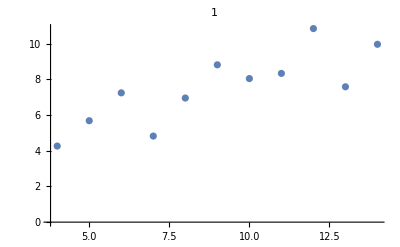
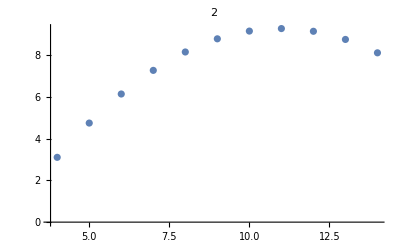
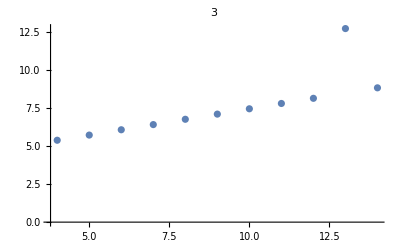
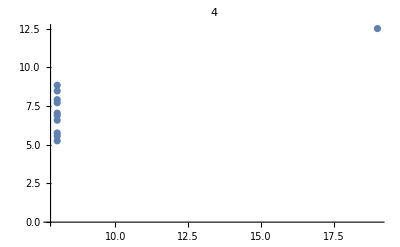

```mathematica
GroupBy[Normal@Normal@Transpose@dsAnscombe,StringSplit[#⟦1⟧,""]⟦2⟧&]
KeyValueMap[ListPlot[Transpose@Values[#2],PlotLabel->#1]&,%]
```

## References

Wide and narrow data - Wikipedia

[AA1] Anton Antonov, Contingency tables creation examples | Mathematica for prediction algorithms

[AAv1] Anton Antonov, "Data Transformation Workflows with Anton Antonov, Session #1", (2020), Wolfram channel at YouTube.

[AAv2] Anton Antonov, "Data Transformation Workflows with Anton Antonov, Session #2", (2020), Wolfram channel at YouTube.

[AAv3] Anton Antonov, "Multi-language Data-Wrangling Conversational Agent", (2021), Wolfram Technology Conference 2020 presentation, Wolfram channel at YouTube.

Related Guides

Data reshaping functions

Related Tech Notes

Data transformation workflows

Long form data transformation

## Metadata

### Categorization

Tech Note

AntonAntonov/DataReshapers

AntonAntonov`DataReshapers`

AntonAntonov/DataReshapers/tutorial/Wideformdatatransformation

### Keywords

Cross tabulation

Contingency matrix

Contingency table

Data transformation

Long form

Wide form